## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PSERT";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)


(* user will need to change this path *)
pathMASSef = "C:/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_PSERT_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:C:\MASSef\examples\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName,  assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{3php,Km or S05 substrate}

{0.000015,Km or S05 value}

{{{3php,Null}},kcat substrates}

{1.75,kcat value}

{3php,Other parameter susbtrate}

{2700,Other parameter value}

{pser,Km or S05 substrate}

{0.000017,Km or S05 value}

{{{pser,Null}},kcat substrates}

{0.39,kcat value}

{pser,Other parameter susbtrate}

{5940,Other parameter value}

{3php,Null;glu,Null;,Keq substrate}

{87.5,Keq value}

((3php)^c+glu^c⇌akg^c+pser^c)^PSERT

Null;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3php,Null;glu,Null; | 87.5 | 83.125
91.875 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3php | 0.000015 | 0.00001425
0.00001575 | glu | 0.000125 | M | 8.2 | 37 | kpi | 0.1 | k | 0.004
f | 0.004
1 | pser | 0.000017 | 0.00001615
0.00001785 | akg | 0.000125 | M | 8.2 | 37 | kpi | 0.1 | k | 0.004
f | 0.004

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3php | Null | 1.75 | 1.6625
1.8375 | 1/s | 8.2 | 37 | kpi | 0.1 | k | 0.004
f | 0.004
1 | pser | Null | 0.39 | 0.3705
0.4095 | 1/s | 8.2 | 37 | kpi | 0.1 | k | 0.004
f | 0.004

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | vmax | 3php | 2700 | 2565.
2835. | glu | 0.000125 | U/mg | 8.2 | 37 | kpi | 0.1 | k | 0.004
f | 0.004
1 | vmax | pser | 5940 | 5643.
6237. | akg | 0.000125 | U/mg | 8.2 | 37 | kpi | 0.1 | k | 0.004
f | 0.004

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)


KeqPriorities = {1};
kmPriorities = {1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = {0,0};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((3php)^c+glu^c⇌akg^c+pser^c)^PSERT

Null;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3php,Null;glu,Null; | 87.5 | 83.125
91.875 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3php | 0.000015 | 0.00001425
0.00001575 | glu | 0.000125 | M | 8.2 | 37 | kpi | 0.1 | k | 0.004
f | 0.004
1 | pser | 0.000017 | 0.00001615
0.00001785 | akg | 0.000125 | M | 8.2 | 37 | kpi | 0.1 | k | 0.004
f | 0.004

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3php | Null | 1.75 | 1.6625
1.8375 | 1/s | 8.2 | 37 | kpi | 0.1 | k | 0.004
f | 0.004
1 | pser | Null | 0.39 | 0.3705
0.4095 | 1/s | 8.2 | 37 | kpi | 0.1 | k | 0.004
f | 0.004

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_PSERT[c] + 3php[c] <=> E_PSERT[c]&3php",
				"E_PSERT[c]&3php + glu[c] <=> E_PSERT[c]&3php&glu",
				"E_PSERT[c]&3php&glu <=> E_PSERT[c]&pser&akg",
				"E_PSERT[c]&pser&akg <=> E_PSERT[c]&pser + akg[c]",
				"E_PSERT[c]&pser <=> E_PSERT[c] + pser[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PSERT^c)_^+(3php)^c⇌(PSERT^c&(3php)^c)_^)^PSERT1,((PSERT^c&pser^c)_^⇌(PSERT^c)_^+pser^c)^PSERT2,((PSERT^c&(3php)^c)_^+glu^c⇌(PSERT^c&(3php)^c&glu^c)_^)^PSERT3,((PSERT^c&pser^c&akg^c)_^⇌(PSERT^c&pser^c)_^+akg^c)^PSERT4,((PSERT^c&(3php)^c&glu^c)_^⇌(PSERT^c&pser^c&akg^c)_^)^PSERT5}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PSERT^c)_^+(3php)^c⇌(PSERT^c&(3php)^c)_^)^PSERT1,Overscript[(PSERT^c&pser^c)_^⇌(PSERT^c)_^+pser^c, PSERT2],((PSERT^c&(3php)^c)_^+glu^c⇌(PSERT^c&(3php)^c&glu^c)_^)^PSERT3,Overscript[(PSERT^c&pser^c&akg^c)_^⇌(PSERT^c&pser^c)_^+akg^c, PSERT4],((PSERT^c&(3php)^c&glu^c)_^⇌(PSERT^c&pser^c&akg^c)_^)^PSERT5};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{(3php)^c→0,glu^c→0}

{akg^c→0,pser^c→0}

{(3php)^c→∞,glu^c→∞}

{akg^c→∞,pser^c→∞}

Added inhibition reactions:

{}

Generating flux equation...

{((PSERT^c&(3php)^c&glu^c)_^-((PSERT^c&pser^c&akg^c)_^)/K_PSERT5) Volume_c k_PSERT5^⟶}

Volume_c (-(PSERT^c&pser^c&akg^c)_^ k_PSERT5^⟵+(PSERT^c&(3php)^c&glu^c)_^ k_PSERT5^⟶)

1

2

3

0.257715

4

0.0004707

5

0.

Simplifying...

6

0.12032

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Part::partw: Part 1 of {} does not exist.

Simulating kcat data...

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
FilePrint@dataPathList
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"C:\MASSef\examples\fit_GAPD_typeII\input\relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	37	"C:\MASSef\examples\fit_GAPD_typeII\input\absRateFor.txt"	1059.363016156407
1	0	0.01	0.01	0	0.01	1	8.9	37	"C:\MASSef\examples\fit_GAPD_typeII\input\absRateFor.txt"	1059.363016156407
1	0	0.01	0.01	0	0.01	1	8.9	37	"C:\MASSef\examples\fit_GAPD_typeII\input\absRateFor.txt"	1059.363016156407
1	0	0.01	0.01	0	0.01	1	8.9	37	"C:\MASSef\examples\fit_GAPD_typeII\input\absRateFor.txt"	1059.363016156407
1	0	0.01	0.01	0	0.01	1	8.9	37	"C:\MASSef\examples\fit_GAPD_typeII\input\absRateFor.txt"	1059.363016156407
1	0	0.01	0.01	0	0.01	1	8.9	37	"C:\MASSef\examples\fit_GAPD_typeII\input\absRateFor.txt"	1059.363016156407
1	0	0.01	0.01	0	0.01	1	8.9	37	"C:\MASSef\examples\fit_GAPD_typeII\input\absRateFor.txt"	1059.363016156407
1	0	0.01	0.01	0	0.01	1	8.9	37	"C:\MASSef\examples\fit_GAPD_typeII\input\absRateFor.txt"	1059.363016156407
1	0	0.01	0.01	0	0.01	1	8.9	37	"C:\MASSef\examples\fit_GAPD_typeII\input\absRateFor.txt"	1059.363016156407
1	0	0.01	0.01	0	0.01	1	8.9	37	"C:\MASSef\examples\fit_GAPD_typeII\input\absRateFor.txt"	1059.363016156407
1	0	0.01	0.01	0	0.01	1	8.9	37	"C:\MASSef\examples\fit_GAPD_typeII\input\absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_typeII\input\customRatio_1.txt"	425.

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
0.7	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
0.7	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
0.7	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
0.7	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
0.7	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
0.7	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
0.7	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
0.7	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
0.7	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
0.7	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
0.7	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
0.7	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
0.7	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
0.7	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
0.7	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
0.7	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
0.7	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
0.7	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
0.7	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
0.7	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
0.7	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
0.7	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[C:\MASSef\examples\fit_PSERT_typeII\input\absRateFor.txt, C:\MASSef\examples\fit_PSERT_typeII\input\absRateRev.txt, C:\MASSef\examples\fit_PSERT_typeII\input\relRateFor_3php.txt, C:\MASSef\examples\fit_PSERT_typeII\input\relRateFor_glu.txt, C:\MASSef\examples\fit_PSERT_typeII\input\relRateRev_akg.txt, C:\MASSef\examples\fit_PSERT_typeII\input\relRateRev_pser.txt, C:\MASSef\examples\fit_PSERT_typeII\input\haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateFor_g3p.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateFor_nad.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateFor_pi.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateRev_13dpg.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateRev_nadh.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\haldaneRatio_1.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\KdRatio_nad.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 1.03647090902
best_fit: 0.973852972574
best_fit: 1.02238055093
best_fit: 1.00398333618
best_fit: 1.0776884493

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 4.31366×10^-12 | 1.86077×10^-23 | 8.69136×10^-10 | 9.93298×10^-10 | 87.5 | 87.5
1 | haldaneRatio_1 | 4.31366×10^-12 | 1.86077×10^-23 | 8.69136×10^-10 | 9.93298×10^-10 | 87.5 | 87.5
1 | haldaneRatio_1 | 4.31366×10^-12 | 1.86077×10^-23 | 8.69136×10^-10 | 9.93298×10^-10 | 87.5 | 87.5
1 | haldaneRatio_1 | 4.31366×10^-12 | 1.86077×10^-23 | 8.69136×10^-10 | 9.93298×10^-10 | 87.5 | 87.5
1 | haldaneRatio_1 | 4.31366×10^-12 | 1.86077×10^-23 | 8.69136×10^-10 | 9.93298×10^-10 | 87.5 | 87.5
1 | haldaneRatio_1 | 4.31366×10^-12 | 1.86077×10^-23 | 8.69136×10^-10 | 9.93298×10^-10 | 87.5 | 87.5
1 | haldaneRatio_1 | 4.31366×10^-12 | 1.86077×10^-23 | 8.69136×10^-10 | 9.93298×10^-10 | 87.5 | 87.5
1 | haldaneRatio_1 | 4.31366×10^-12 | 1.86077×10^-23 | 8.69136×10^-10 | 9.93298×10^-10 | 87.5 | 87.5
1 | haldaneRatio_1 | 4.31366×10^-12 | 1.86077×10^-23 | 8.69136×10^-10 | 9.93298×10^-10 | 87.5 | 87.5
1 | haldaneRatio_1 | 4.31366×10^-12 | 1.86077×10^-23 | 8.69136×10^-10 | 9.93298×10^-10 | 87.5 | 87.5
1 | haldaneRatio_1 | 4.31366×10^-12 | 1.86077×10^-23 | 8.69136×10^-10 | 9.93298×10^-10 | 87.5 | 87.5
1 | relRateFor_3php | 2.81042×10^-12 | 7.89845×10^-24 | 5.88266×10^-13 | 6.47092×10^-10 | 0.0909091 | 0.0909091
1 | relRateFor_3php | 2.66842×10^-12 | 7.12047×10^-24 | 8.40578×10^-13 | 6.14426×10^-10 | 0.136807 | 0.136807
1 | relRateFor_3php | 2.4708×10^-12 | 6.10486×10^-24 | 1.14217×10^-12 | 5.68923×10^-10 | 0.20076 | 0.20076
1 | relRateFor_3php | 2.21112×10^-12 | 4.88905×10^-24 | 1.44973×10^-12 | 5.09128×10^-10 | 0.284747 | 0.284747
1 | relRateFor_3php | 1.89543×10^-12 | 3.59265×10^-24 | 1.68843×10^-12 | 4.3644×10^-10 | 0.386863 | 0.386863
1 | relRateFor_3php | 1.5456×10^-12 | 2.38887×10^-24 | 1.77947×10^-12 | 3.55893×10^-10 | 0.5 | 0.5
1 | relRateFor_3php | 1.19593×10^-12 | 1.43025×10^-24 | 1.68843×10^-12 | 2.75375×10^-10 | 0.613137 | 0.613137
1 | relRateFor_3php | 8.80268×10^-13 | 7.74872×10^-25 | 1.44973×10^-12 | 2.02688×10^-10 | 0.715253 | 0.715253
1 | relRateFor_3php | 6.20531×10^-13 | 3.85059×10^-25 | 1.14198×10^-12 | 1.42883×10^-10 | 0.79924 | 0.79924
1 | relRateFor_3php | 4.22953×10^-13 | 1.7889×10^-25 | 8.40661×10^-13 | 9.73897×10^-11 | 0.863193 | 0.863193
1 | relRateFor_3php | 2.80949×10^-13 | 7.89323×10^-26 | 5.88085×10^-13 | 6.46894×10^-11 | 0.909091 | 0.909091
1 | relRateRev_pser | 1.83409×10^-12 | 3.36388×10^-24 | 3.83901×10^-13 | 4.22291×10^-10 | 0.0909091 | 0.0909091
1 | relRateRev_pser | 1.7415×10^-12 | 3.03281×10^-24 | 5.48589×10^-13 | 4.00995×10^-10 | 0.136807 | 0.136807
1 | relRateRev_pser | 1.61238×10^-12 | 2.59976×10^-24 | 7.45348×10^-13 | 3.71263×10^-10 | 0.20076 | 0.20076
1 | relRateRev_pser | 1.44296×10^-12 | 2.08212×10^-24 | 9.46021×10^-13 | 3.32232×10^-10 | 0.284747 | 0.284747
1 | relRateRev_pser | 1.23707×10^-12 | 1.53033×10^-24 | 1.10195×10^-12 | 2.84843×10^-10 | 0.386863 | 0.386863
1 | relRateRev_pser | 1.00875×10^-12 | 1.01757×10^-24 | 1.1614×10^-12 | 2.32281×10^-10 | 0.5 | 0.5
1 | relRateRev_pser | 7.8057×10^-13 | 6.0929×10^-25 | 1.10201×10^-12 | 1.79733×10^-10 | 0.613137 | 0.613137
1 | relRateRev_pser | 5.74429×10^-13 | 3.29969×10^-25 | 9.46021×10^-13 | 1.32264×10^-10 | 0.715253 | 0.715253
1 | relRateRev_pser | 4.05107×10^-13 | 1.64111×10^-25 | 7.45515×10^-13 | 9.3278×10^-11 | 0.79924 | 0.79924
1 | relRateRev_pser | 2.76001×10^-13 | 7.61768×10^-26 | 5.48561×10^-13 | 6.35502×10^-11 | 0.863193 | 0.863193
1 | relRateRev_pser | 1.83513×10^-13 | 3.3677×10^-26 | 3.84137×10^-13 | 4.22551×10^-11 | 0.909091 | 0.909091
1 | absRateFor | 3.41255×10^-13 | 1.16455×10^-25 | 1.37512×10^-12 | 7.85784×10^-11 | 1.75 | 1.75
1 | absRateFor | 3.41255×10^-13 | 1.16455×10^-25 | 1.37512×10^-12 | 7.85784×10^-11 | 1.75 | 1.75
1 | absRateFor | 3.41255×10^-13 | 1.16455×10^-25 | 1.37512×10^-12 | 7.85784×10^-11 | 1.75 | 1.75
1 | absRateFor | 3.41255×10^-13 | 1.16455×10^-25 | 1.37512×10^-12 | 7.85784×10^-11 | 1.75 | 1.75
1 | absRateFor | 3.41255×10^-13 | 1.16455×10^-25 | 1.37512×10^-12 | 7.85784×10^-11 | 1.75 | 1.75
1 | absRateFor | 3.41255×10^-13 | 1.16455×10^-25 | 1.37512×10^-12 | 7.85784×10^-11 | 1.75 | 1.75
1 | absRateFor | 3.41255×10^-13 | 1.16455×10^-25 | 1.37512×10^-12 | 7.85784×10^-11 | 1.75 | 1.75
1 | absRateFor | 3.41255×10^-13 | 1.16455×10^-25 | 1.37512×10^-12 | 7.85784×10^-11 | 1.75 | 1.75
1 | absRateFor | 3.41255×10^-13 | 1.16455×10^-25 | 1.37512×10^-12 | 7.85784×10^-11 | 1.75 | 1.75
1 | absRateFor | 3.41255×10^-13 | 1.16455×10^-25 | 1.37512×10^-12 | 7.85784×10^-11 | 1.75 | 1.75
1 | absRateFor | 3.41255×10^-13 | 1.16455×10^-25 | 1.37512×10^-12 | 7.85784×10^-11 | 1.75 | 1.75
1 | absRateRev | 1.93567×10^-13 | 3.74683×10^-26 | 1.73805×10^-13 | 4.45655×10^-11 | 0.39 | 0.39
1 | absRateRev | 1.93567×10^-13 | 3.74683×10^-26 | 1.73805×10^-13 | 4.45655×10^-11 | 0.39 | 0.39
1 | absRateRev | 1.93567×10^-13 | 3.74683×10^-26 | 1.73805×10^-13 | 4.45655×10^-11 | 0.39 | 0.39
1 | absRateRev | 1.93567×10^-13 | 3.74683×10^-26 | 1.73805×10^-13 | 4.45655×10^-11 | 0.39 | 0.39
1 | absRateRev | 1.93567×10^-13 | 3.74683×10^-26 | 1.73805×10^-13 | 4.45655×10^-11 | 0.39 | 0.39
1 | absRateRev | 1.93567×10^-13 | 3.74683×10^-26 | 1.73805×10^-13 | 4.45655×10^-11 | 0.39 | 0.39
1 | absRateRev | 1.93567×10^-13 | 3.74683×10^-26 | 1.73805×10^-13 | 4.45655×10^-11 | 0.39 | 0.39
1 | absRateRev | 1.93567×10^-13 | 3.74683×10^-26 | 1.73805×10^-13 | 4.45655×10^-11 | 0.39 | 0.39
1 | absRateRev | 1.93567×10^-13 | 3.74683×10^-26 | 1.73805×10^-13 | 4.45655×10^-11 | 0.39 | 0.39
1 | absRateRev | 1.93567×10^-13 | 3.74683×10^-26 | 1.73805×10^-13 | 4.45655×10^-11 | 0.39 | 0.39
1 | absRateRev | 1.93567×10^-13 | 3.74683×10^-26 | 1.73805×10^-13 | 4.45655×10^-11 | 0.39 | 0.39

### Simulated Data and Best Fit Data Plot

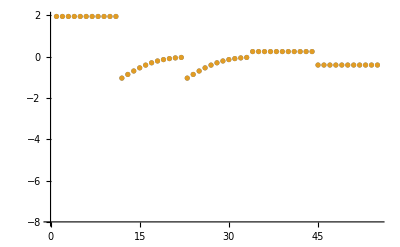

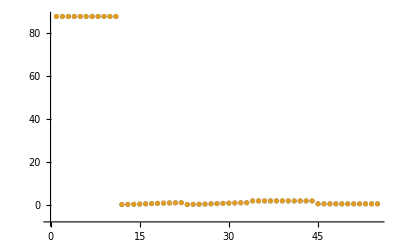

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

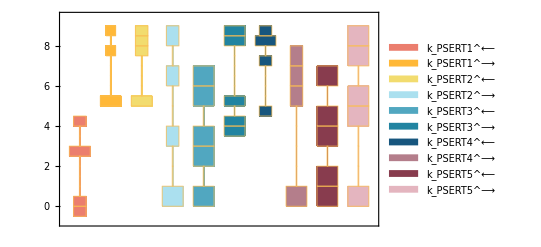

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

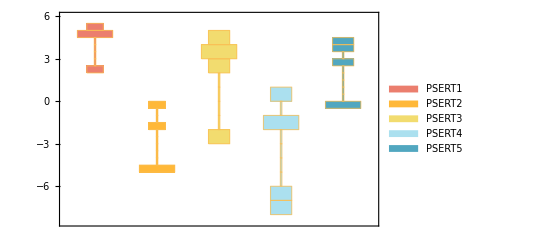

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

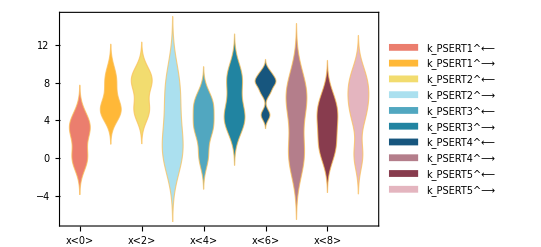

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 2.51272×10^-6
0.00089 | 0.00089 | 1.39821×10^-6
0.00053 | 0.00053 | 1.35758×10^-6

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 3.33383×10^-6

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 8.29398×10^-6

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452 | 4.57492×10^-6